```mathematica
Llist[g_,L_] := Table [ - g^2/(2) ,2 L] 
 Ldown[g_,L_] := DiagonalMatrix[Llist[g,L],1]
Lup[g_,L_] := DiagonalMatrix[Llist[g,L],-1]
LzLz[g_,L_] := DiagonalMatrix[Table[m^2 /g^2  +  g^2,{m,-L, L }] ]
FluxPlaqOperator[g_,L_]  := LzLz[g,L]+  Ldown[g,L]+  Lup[g,L]
```

```mathematica
HSG[b_, h_, L_, Nsites_]:= (1/2)Sum[KroneckerProduct@@Table[If[j==i, LzLz[1, L], IdentityMatrix[2L+1]], {j, 1, Nsites}], {i, 1, Nsites}]-b Sum[KroneckerProduct@@Table[If[j==i||j==i+1, If[j==i, Lup[1,L] , Ldown[1, L]], IdentityMatrix[2L+1]], {j, 1, Nsites}], {i, 1, Nsites-1}]-b Sum[KroneckerProduct@@Table[If[j==i||j==i+1, If[j==i, Ldown[1,L] , Lup[1, L]], IdentityMatrix[2L+1]], {j, 1, Nsites}], {i, 1, Nsites-1}]-(h /2)Sum[KroneckerProduct@@Table[If[j==i, Ldown[1,L] +Lup[1, L], IdentityMatrix[2L+1]], {j, 1, Nsites}], {i, 1, Nsites}]
```

```mathematica
Cosx[x_, state_, b_, h_, L_, Nsites_]:=(
{evals, evecs}=Eigensystem[HSG[b, h, L, Nsites]//N];
evecs=(Normalize/@evecs[[Ordering[evals]]]);
Return[evecs[[state]].KroneckerProduct@@Table[If[j==x, Ldown[1,L] +Lup[1, L], IdentityMatrix[2L+1]], {j, 1, Nsites}].evecs[[state]]/2.0];)
```

```mathematica
Sinx[x_, state_, b_, h_, L_, Nsites_]:=(
{evals, evecs}=Eigensystem[HSG[b, h, L, Nsites]//N];
evecs=(Normalize/@evecs[[Ordering[evals]]]);
Return[evecs[[state]].KroneckerProduct@@Table[If[j==x, Ldown[1,L] -Lup[1, L], IdentityMatrix[2L+1]], {j, 1, Nsites}].evecs[[state]]/(2.0 I)];)
```

```mathematica
Mh[b_, h_, L_, Nsites_]:=(
{evals, evecs}=Eigensystem[HSG[b, h, L, Nsites]//N];
evecs=(Normalize/@evecs[[Ordering[evals]]]);
Return[evecs[[1]].Sum[KroneckerProduct@@Table[If[j==i, Ldown[1,L] +Lup[1, L], IdentityMatrix[2L+1]], {j, 1, Nsites}], {i, 1, Nsites}].evecs[[1]]];)
```

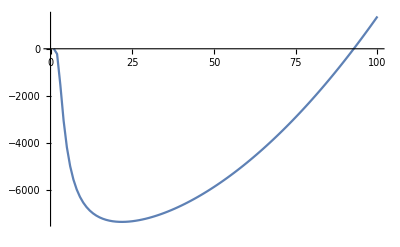

```mathematica
h=4 10^(-5);
delh = 10^(-8);
(*ListPlot[Table[{b, Mh[b, h, 1, 4]}, {b, 0.01, 2, 0.01}], Joined->True, PlotRange->All]*)
mu=Table[(Mh[b, h+delh, 1, 4]-Mh[b, h-delh, 1, 4])/(2 delh), {b, 0.01, 100, 1}];
bList = Table[b, {b, 0.01, 100, 1}];
ListPlot[bList^2(1-mu/bList-mu^2), Joined->True, PlotRange->All]
```

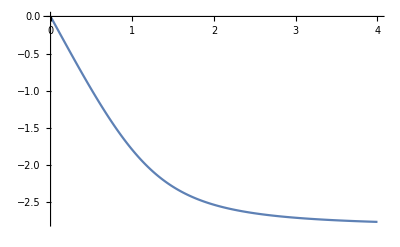

```mathematica
ListPlot[Table[{h, Mh[1, h, 1, 4]}, {h ,0.01, 4, 0.01}], Joined->True, PlotRange->All]
```

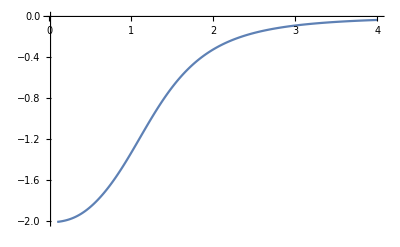

```mathematica
ListPlot[Table[{h, (Mh[1, h+delh, 1, 4]-Mh[1, h-delh, 1, 4])/(2 delh)}, {h, 0.1, 4, 0.001}], Joined->True, PlotRange->All]
```

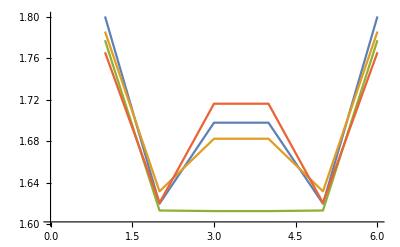

```mathematica
Nsites=6;
ListPlot[Table[Table[ArcCos[Cosx[x, state, 1, 1, 1, Nsites]], {x, 1, Nsites}], {state, 1, 4}], Joined->True]
```

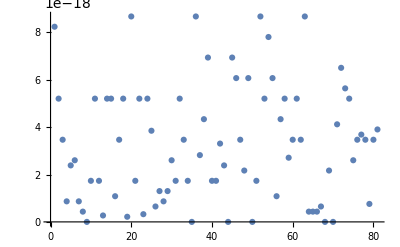

```mathematica
ListPlot[Table[ArcSin[Abs[Sinx[1, state, 1, 1, 1, 4]]], {state, 1, 3^4}]]
```

```mathematica
Eigenvalues[Lup[1, 2]-Ldown[1, 2]]
```

{(ⅈ √3)/2,-(ⅈ √3)/2,ⅈ/2,-ⅈ/2,0}